```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,p,q,r,f,g,h,e,i,j,k,l]
```

```mathematica
s=s/.Solve[1/p+1/q+1/r+1/s-1==0,s][[1]]
```

(p q r)/(-p q-p r-q r+p q r)

```mathematica
f[p_,i_]=Exp[2*Pi*I*i/p]
```

ⅇ^((2 ⅈ i π)/p)

```mathematica
g[q_,j_]=Exp[2*Pi*I*j/q]
```

ⅇ^((2 ⅈ j π)/q)

```mathematica
h[r_,k_]=Exp[2*Pi*I*k/r]
```

ⅇ^((2 ⅈ k π)/r)

```mathematica
e[s_,l_]=Exp[2*Pi*I*l/s]/.p->2/.q->3/.r->7
```

ⅇ^((ⅈ l π)/21)

```mathematica
wf=Union[Flatten[Table[N[f[2,i]*g[3,j]*h[7,k]*e[42,l]],{i,0,1},{j,0,2},{k,0,6},{l,0,41}]]];
```

```mathematica
Length[wf]
```

78

```mathematica
ComplexListPlot[wf,ColorFunction->Hue,ImageSize->2000];
```

```mathematica
(*Projective Plane*)
```

```mathematica
pl=Table[Re[wf[[i]]]/(1+Im[wf[[i]]]),{i,Length[wf]}]
```

{-1.,-1.16202,-0.86057,-1.16202,-0.86057,-1.35495,-0.738034,-1.59149,-0.628342,-1.59149,-0.628342,-1.89209,-0.528515,-1.89209,-0.528515,-2.29202,-0.436296,-2.29202,-0.436296,-2.85784,-0.349915,-2.85784,-0.349915,-3.73205,-0.267949,-3.73205,-0.267949,-5.28513,-0.18921,-5.28513,-0.18921,-8.87525,-0.112673,-8.87525,-0.112673,-26.7256,-0.0374174,-26.7256,-0.0374174,26.7256,0.0374174,26.7256,0.0374174,8.87525,0.112673,8.87525,0.112673,5.28513,0.18921,5.28513,0.18921,3.73205,0.267949,3.73205,0.267949,2.85784,0.349915,2.85784,0.349915,2.29202,0.436296,2.29202,0.436296,1.89209,0.528515,1.89209,0.528515,1.59149,0.628342,1.59149,0.628342,1.35495,0.738034,1.16202,0.86057,1.16202,0.86057,1.}

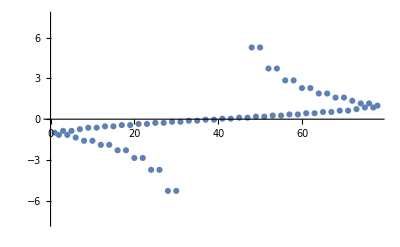

```mathematica
ListPlot[pl]
```

```mathematica
(*continued fractions*)
```

```mathematica
cf=Table[ContinuedFraction[N[pl[[i]],50]],{i,Length[pl]}]
```

ContinuedFraction::start: Warning: ContinuedFraction was unable to obtain at least one term using precision 15.9546.

{ContinuedFraction[-1.],{-1,-6,-5,-1,-4,-2,-1,-16,-1,-1,-2,-4,-1,-1,-4,-2,-2},{0,-1,-6,-5,-1,-4,-2,-1,-16,-1,-1,-2,-4,-1,-1,-4,-2,-2},{-1,-6,-5,-1,-4,-2,-1,-16,-1,-1,-2,-4,-1,-1,-4,-2,-2,-3},{0,-1,-6,-5,-1,-4,-2,-1,-16,-1,-1,-2,-4,-1,-1,-4,-2,-2},{-1,-2,-1,-4,-2,-8,-1,-2,-1,-7,-1,-22,-2,-2,-3,-1},{0,-1,-2,-1,-4,-2,-8,-1,-2,-1,-7,-1,-22,-2,-2,-3,-1},{-1,-1,-1,-2,-4,-3,-3,-11,-1,-1,-1,-1,-47,-3,-2,-2,-1},{0,-1,-1,-1,-2,-4,-3,-3,-11,-1,-1,-1,-1,-47,-3,-2,-2,-1},{-1,-1,-1,-2,-4,-3,-3,-11,-1,-1,-1,-1,-47,-3,-2,-2,-1},{0,-1,-1,-1,-2,-4,-3,-3,-11,-1,-1,-1,-1,-47,-3,-2,-2,-1},{-1,-1,-8,-3,-1,-2,-1,-7,-1,-7,-25,-1,-2,-3,-1,-1,-1},{0,-1,-1,-8,-3,-1,-2,-1,-7,-1,-7,-25,-1,-2,-3,-1,-1,-1},{-1,-1,-8,-3,-1,-2,-1,-7,-1,-7,-25,-1,-2,-3,-1,-1,-1},{0,-1,-1,-8,-3,-1,-2,-1,-7,-1,-7,-25,-1,-2,-3,-1,-1,-1},{-2,-3,-2,-2,-1,-4,-6,-1,-6,-1,-15,-1,-1,-1,-8,-1,-1},{0,-2,-3,-2,-2,-1,-4,-6,-1,-6,-1,-15,-1,-1,-1,-8,-1,-1},{-2,-3,-2,-2,-1,-4,-6,-1,-6,-1,-15,-1,-1,-1,-8,-1,-1},{0,-2,-3,-2,-2,-1,-4,-6,-1,-6,-1,-15,-1,-1,-1,-8,-1,-1},{-2,-1,-6,-29,-3,-4,-11,-1,-2,-1,-25,-1},{0,-2,-1,-6,-29,-3,-4,-11,-1,-2,-1,-25,-1},{-2,-1,-6,-29,-3,-4,-11,-1,-2,-1,-25,-1,-7},{0,-2,-1,-6,-29,-3,-4,-11,-1,-2,-1,-25,-1,-7},{-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{0,-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{0,-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{-5,-3,-1,-1,-34,-5,-2,-2,-1,-1,-1,-76,-4},{0,-5,-3,-1,-1,-34,-5,-2,-2,-1,-1,-1,-76,-4,-1},{-5,-3,-1,-1,-34,-5,-2,-2,-1,-1,-1,-76,-5},{0,-5,-3,-1,-1,-34,-5,-2,-2,-1,-1,-1,-76,-4,-1},{-8,-1,-7,-63,-1,-1,-8,-1,-2,-1,-1,-2,-3,-3,-1,-1},{0,-8,-1,-7,-63,-1,-1,-8,-1,-2,-1,-1,-2,-3,-3,-1,-1,-2},{-8,-1,-7,-63,-1,-1,-8,-1,-2,-1,-1,-2,-3,-3,-1,-1,-2,-1},{0,-8,-1,-7,-63,-1,-1,-8,-1,-2,-1,-1,-2,-3,-3,-1,-1},{-26,-1,-2,-1,-1,-1,-4,-5,-10,-1,-13,-1,-2,-1,-2,-6},{0,-26,-1,-2,-1,-1,-1,-4,-5,-10,-1,-13,-1,-2,-1,-2,-5,-3},{-26,-1,-2,-1,-1,-1,-4,-5,-10,-1,-13,-1,-2,-1,-2,-6,-2},{0,-26,-1,-2,-1,-1,-1,-4,-5,-10,-1,-13,-1,-2,-1,-2,-5},{26,1,2,1,1,1,4,5,10,1,13,1,2,1,2,6,2},{0,26,1,2,1,1,1,4,5,10,1,13,1,2,1,2,5},{26,1,2,1,1,1,4,5,10,1,13,1,2,1,2,6},{0,26,1,2,1,1,1,4,5,10,1,13,1,2,1,2,5,3},{8,1,7,63,1,1,8,1,2,1,1,2,3,3,1,1,2,1},{0,8,1,7,63,1,1,8,1,2,1,1,2,3,3,1,1},{8,1,7,63,1,1,8,1,2,1,1,2,3,3,1,1},{0,8,1,7,63,1,1,8,1,2,1,1,2,3,3,1,1,2},{5,3,1,1,34,5,2,2,1,1,1,76,5},{0,5,3,1,1,34,5,2,2,1,1,1,76,4,1},{5,3,1,1,34,5,2,2,1,1,1,76,4},{0,5,3,1,1,34,5,2,2,1,1,1,76,4,1},{3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1},{0,3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1},{3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2},{0,3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2},{2,1,6,29,3,4,11,1,2,1,25,1,7},{0,2,1,6,29,3,4,11,1,2,1,25,1,7},{2,1,6,29,3,4,11,1,2,1,25,1},{0,2,1,6,29,3,4,11,1,2,1,25,1},{2,3,2,2,1,4,6,1,6,1,15,1,1,1,8,1,1},{0,2,3,2,2,1,4,6,1,6,1,15,1,1,1,8,1,1},{2,3,2,2,1,4,6,1,6,1,15,1,1,1,8,1,1},{0,2,3,2,2,1,4,6,1,6,1,15,1,1,1,8,1,1},{1,1,8,3,1,2,1,7,1,7,25,1,2,3,1,1,1},{0,1,1,8,3,1,2,1,7,1,7,25,1,2,3,1,1,1},{1,1,8,3,1,2,1,7,1,7,25,1,2,3,1,1,1},{0,1,1,8,3,1,2,1,7,1,7,25,1,2,3,1,1,1},{1,1,1,2,4,3,3,11,1,1,1,1,47,3,2,2,1},{0,1,1,1,2,4,3,3,11,1,1,1,1,47,3,2,2,1},{1,1,1,2,4,3,3,11,1,1,1,1,47,3,2,2,1},{0,1,1,1,2,4,3,3,11,1,1,1,1,47,3,2,2,1},{1,2,1,4,2,8,1,2,1,7,1,22,2,2,3,1},{0,1,2,1,4,2,8,1,2,1,7,1,22,2,2,3,1},{1,6,5,1,4,2,1,16,1,1,2,4,1,1,4,2,2},{0,1,6,5,1,4,2,1,16,1,1,2,4,1,1,4,2,2},{1,6,5,1,4,2,1,16,1,1,2,4,1,1,4,2,2,3},{0,1,6,5,1,4,2,1,16,1,1,2,4,1,1,4,2,2},ContinuedFraction[1.]}

```mathematica
(*Rational Continued fractions*)
```

```mathematica
w=Union[Table[FromContinuedFraction[cf[[i]]],{i,2,Length[cf]-1}]]
```

{-81530792/3050667,-175872429/6580682,-38591369/4348203,-137611968/15505145,-50877535/9626549,-40728516/7706251,-29354524/7865521,-80198051/21489003,-9816646/3434993,-78166119/27351508,-13348720/5823987,-16837217/8898729,-25583991/16075487,-6927243/5112538,-47647703/41004164,-13980809/12031459,-12031459/13980809,-5112538/6927243,-16075487/25583991,-8898729/16837217,-5823987/13348720,-27351508/78166119,-3434993/9816646,-21489003/80198051,-7865521/29354524,-9626549/50877535,-11156942/99020599,-4348203/38591369,-8193305/218970686,-2571319/68719947,2571319/68719947,8193305/218970686,4348203/38591369,11156942/99020599,9626549/50877535,7865521/29354524,21489003/80198051,3434993/9816646,27351508/78166119,5823987/13348720,8898729/16837217,16075487/25583991,5112538/6927243,12031459/13980809,13980809/12031459,47647703/41004164,6927243/5112538,25583991/16075487,16837217/8898729,13348720/5823987,78166119/27351508,9816646/3434993,80198051/21489003,29354524/7865521,40728516/7706251,50877535/9626549,137611968/15505145,38591369/4348203,175872429/6580682,81530792/3050667}

```mathematica
N[w]
```

{-26.7256,-26.7256,-8.87525,-8.87525,-5.28513,-5.28513,-3.73205,-3.73205,-2.85784,-2.85784,-2.29202,-1.89209,-1.59149,-1.35495,-1.16202,-1.16202,-0.86057,-0.738034,-0.628342,-0.528515,-0.436296,-0.349915,-0.349915,-0.267949,-0.267949,-0.18921,-0.112673,-0.112673,-0.0374174,-0.0374174,0.0374174,0.0374174,0.112673,0.112673,0.18921,0.267949,0.267949,0.349915,0.349915,0.436296,0.528515,0.628342,0.738034,0.86057,1.16202,1.16202,1.35495,1.59149,1.89209,2.29202,2.85784,2.85784,3.73205,3.73205,5.28513,5.28513,8.87525,8.87525,26.7256,26.7256}

```mathematica
Length[w]
```

60

```mathematica
f1[z_,i_]:=N[-Exp[2*π*I*w[[i]]]*z^2*(z−4)/(1−4z),100]
```

```mathematica
g1=Flatten[ParallelTable[{JuliaSetPlot[f1[z,i],z,ImageSize->{940,560},PlotRange->{{-4.05,7.55},{-5.8,5.8}},ColorFunction->Hue],JuliaSetPlot[f1[z,i],z,ImageSize->{940,560},PlotRange->{{-4.05,7.55},{-5.8,5.8}},ColorFunction->Hue],JuliaSetPlot[f1[z,i],z,ImageSize->{940,560},PlotRange->{{-4.05,7.55},{-5.8,5.8}},ColorFunction->Hue]},{i,Length[w]}]];
```

```mathematica
Export["Herman_rings_movie3x_Fuchsian_237_42_Hue.mp4",g1]
```

Herman_rings_movie3x_Fuchsian_237_42_Hue.mp4

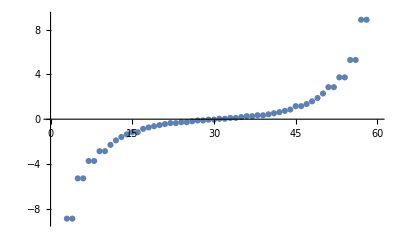

```mathematica
ListPlot[w]
```

```mathematica
(* vector contimued fraction length*)
```

```mathematica
cfl=Table[Length[cf[[i]]],{i,1,Length[cf]}]
```

{1,17,18,18,18,16,17,17,18,17,18,17,18,17,18,17,18,17,18,12,13,13,14,27,28,26,27,13,15,13,15,16,18,18,17,16,18,17,17,17,17,16,18,18,17,16,18,13,15,13,15,26,27,27,28,13,14,12,13,17,18,17,18,17,18,17,18,17,18,17,18,16,17,17,18,18,18,1}

```mathematica
max=Max[cfl]
```

28

```mathematica
Union[Table[If[Length[cf[[i]]]==max,FromContinuedFraction[cf[[i]]],Nothing],{i,Length[cf]}]]
```

{-21489003/80198051,21489003/80198051}

```mathematica
N[%]
```

{-0.267949,0.267949}

```mathematica
(* Maximum cusp*)
```

```mathematica
cfm=Table[Max[cf[[i]]],{i,2,Length[cf]-1}]
```

{-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,26,26,26,26,63,63,63,63,76,76,76,76,3,3,3,3,29,29,29,29,15,15,15,15,25,25,25,25,47,47,47,47,22,22,16,16,16,16}

```mathematica
maxm=Max[cfm]
```

76

```mathematica
Union[Table[If[Max[cf[[i]]]==maxm,FromContinuedFraction[cf[[i]]],Nothing],{i,2,Length[cf]-1}]]

N[%]
```

{9626549/50877535,40728516/7706251,50877535/9626549}

{0.18921,5.28513,5.28513}

```mathematica
(*end*)
```